#### Plus Polarisation Metric

```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M,4,IndexRange[a,n]]
```

ValidateSymbol::used: Symbol M is already used as a manifold.

```mathematica
DefMetric[-1, metric[-a,-b],CD,{";","∇"},PrintAs-> "g"]
```

DefMetric::old: There are already metrics {metric} in vbundle 𝕋M.

ValidateSymbol::used: Symbol metric is already used as a metric.

```mathematica
DefChart[ch,M,{0,1,2,3},{t[],x[],y[],z[]},ChartColor->Blue]
```

ValidateSymbol::used: Symbol ch is already used as a mapping.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

#### GW Metric

```mathematica
MetricInBasis[metric,-ch,{{-1,0,0,0},{0,1+0.2*Cos[t[]],0,0},{0,0,1-0.2*Cos[t[]],0},{0,0,0,1}}]
```

Replaced independent rule g |   |  
1 | 1→1 by g |   |  
1 | 1→1+0.2 Cos[t] for tensor metric

Replaced independent rule g |   |  
1 | 2→-0.2 Cos[t] by g |   |  
1 | 2→0 for tensor metric

Replaced independent rule g |   |  
2 | 2→1 by g |   |  
2 | 2→1-0.2 Cos[t] for tensor metric

{{g |   |  
0 | 0→-1,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→1+0.2 Cos[t],g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→1-0.2 Cos[t],g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→1}}

```mathematica
MetricCompute[metric, ch,All]
```

```mathematica
metric[-a,-b]//ToBasis[ch]//ComponentArray//ToValues//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1+0.2 Cos[t] | 0 | 0
0 | 0 | 1-0.2 Cos[t] | 0
0 | 0 | 0 | 1)

```mathematica
DefTensor[F[-a,b],M]
```

ValidateSymbol::used: Symbol F is already used as a tensor.

#### Deviation Vector (and some other needed tensors)

```mathematica
DefTensor[v[a],M]
```

ValidateSymbol::used: Symbol v is already used as a tensor.

```mathematica
DefTensor[ww[-a,b],M]
```

ValidateSymbol::used: Symbol ww is already used as a tensor.

```mathematica
DefTensor[www[-a,-b, c],M]
```

ValidateSymbol::used: Symbol www is already used as a tensor.

```mathematica
DefTensor[wwww[-a,-b, c],M]
```

ValidateSymbol::used: Symbol wwww is already used as a tensor.

```mathematica
DefScalarFunction[aa]
```

ValidateSymbol::used: Symbol aa is already used as a scalar function.

```mathematica
DefScalarFunction[bb]
```

ValidateSymbol::used: Symbol bb is already used as a scalar function.

```mathematica
DefScalarFunction[cc]
```

ValidateSymbol::used: Symbol cc is already used as a scalar function.

```mathematica
AllComponentValues[v[{a,ch}],{0,aa[t[]],bb[t[]],cc[t[]]}]
```

FoldedRule[{},{v | 0
 →0,v | 1
 →aa[t],v | 2
 →bb[t],v | 3
 →cc[t]}]

```mathematica
$DefInfoQ=False;
$UndefInfoQ=False;
$PrePrint=ScreenDollarIndices;
```

#### LHS of geodesic deviation

```mathematica
CD[-b]@v[c]
%//ToBasis[ch]//ToBasis[ch]//ToCanonical
%//ComponentArray//TraceBasisDummy
%//ToValues//FullSimplify
%//MatrixForm
AllComponentValues[ww[{-a,ch},{b,ch}],%]
CD[-a]@ww[-b,c]
%//ToBasis[ch]//ToBasis[ch]//ToCanonical
%//ComponentArray//TraceBasisDummy
%//ToValues//FullSimplify
%//MatrixForm
AllComponentValues[www[{-a,ch},{-b,ch},{c,ch}],%]
```

∇_b v | c

Γ[∇,𝒟] | c |   |  
  | b | a v | a
 +∇_b v | c

{{Γ[∇,𝒟] | 0 |   |  
  | 0 | 0 v | 0
 +Γ[∇,𝒟] | 0 |   |  
  | 0 | 1 v | 1
 +Γ[∇,𝒟] | 0 |   |  
  | 0 | 2 v | 2
 +Γ[∇,𝒟] | 0 |   |  
  | 0 | 3 v | 3
 +∇_0 v | 0
 ,Γ[∇,𝒟] | 1 |   |  
  | 0 | 0 v | 0
 +Γ[∇,𝒟] | 1 |   |  
  | 0 | 1 v | 1
 +Γ[∇,𝒟] | 1 |   |  
  | 0 | 2 v | 2
 +Γ[∇,𝒟] | 1 |   |  
  | 0 | 3 v | 3
 +∇_0 v | 1
 ,Γ[∇,𝒟] | 2 |   |  
  | 0 | 0 v | 0
 +Γ[∇,𝒟] | 2 |   |  
  | 0 | 1 v | 1
 +Γ[∇,𝒟] | 2 |   |  
  | 0 | 2 v | 2
 +Γ[∇,𝒟] | 2 |   |  
  | 0 | 3 v | 3
 +∇_0 v | 2
 ,Γ[∇,𝒟] | 3 |   |  
  | 0 | 0 v | 0
 +Γ[∇,𝒟] | 3 |   |  
  | 0 | 1 v | 1
 +Γ[∇,𝒟] | 3 |   |  
  | 0 | 2 v | 2
 +Γ[∇,𝒟] | 3 |   |  
  | 0 | 3 v | 3
 +∇_0 v | 3
 },{Γ[∇,𝒟] | 0 |   |  
  | 1 | 0 v | 0
 +Γ[∇,𝒟] | 0 |   |  
  | 1 | 1 v | 1
 +Γ[∇,𝒟] | 0 |   |  
  | 1 | 2 v | 2
 +Γ[∇,𝒟] | 0 |   |  
  | 1 | 3 v | 3
 +∇_1 v | 0
 ,Γ[∇,𝒟] | 1 |   |  
  | 1 | 0 v | 0
 +Γ[∇,𝒟] | 1 |   |  
  | 1 | 1 v | 1
 +Γ[∇,𝒟] | 1 |   |  
  | 1 | 2 v | 2
 +Γ[∇,𝒟] | 1 |   |  
  | 1 | 3 v | 3
 +∇_1 v | 1
 ,Γ[∇,𝒟] | 2 |   |  
  | 1 | 0 v | 0
 +Γ[∇,𝒟] | 2 |   |  
  | 1 | 1 v | 1
 +Γ[∇,𝒟] | 2 |   |  
  | 1 | 2 v | 2
 +Γ[∇,𝒟] | 2 |   |  
  | 1 | 3 v | 3
 +∇_1 v | 2
 ,Γ[∇,𝒟] | 3 |   |  
  | 1 | 0 v | 0
 +Γ[∇,𝒟] | 3 |   |  
  | 1 | 1 v | 1
 +Γ[∇,𝒟] | 3 |   |  
  | 1 | 2 v | 2
 +Γ[∇,𝒟] | 3 |   |  
  | 1 | 3 v | 3
 +∇_1 v | 3
 },{Γ[∇,𝒟] | 0 |   |  
  | 2 | 0 v | 0
 +Γ[∇,𝒟] | 0 |   |  
  | 2 | 1 v | 1
 +Γ[∇,𝒟] | 0 |   |  
  | 2 | 2 v | 2
 +Γ[∇,𝒟] | 0 |   |  
  | 2 | 3 v | 3
 +∇_2 v | 0
 ,Γ[∇,𝒟] | 1 |   |  
  | 2 | 0 v | 0
 +Γ[∇,𝒟] | 1 |   |  
  | 2 | 1 v | 1
 +Γ[∇,𝒟] | 1 |   |  
  | 2 | 2 v | 2
 +Γ[∇,𝒟] | 1 |   |  
  | 2 | 3 v | 3
 +∇_2 v | 1
 ,Γ[∇,𝒟] | 2 |   |  
  | 2 | 0 v | 0
 +Γ[∇,𝒟] | 2 |   |  
  | 2 | 1 v | 1
 +Γ[∇,𝒟] | 2 |   |  
  | 2 | 2 v | 2
 +Γ[∇,𝒟] | 2 |   |  
  | 2 | 3 v | 3
 +∇_2 v | 2
 ,Γ[∇,𝒟] | 3 |   |  
  | 2 | 0 v | 0
 +Γ[∇,𝒟] | 3 |   |  
  | 2 | 1 v | 1
 +Γ[∇,𝒟] | 3 |   |  
  | 2 | 2 v | 2
 +Γ[∇,𝒟] | 3 |   |  
  | 2 | 3 v | 3
 +∇_2 v | 3
 },{Γ[∇,𝒟] | 0 |   |  
  | 3 | 0 v | 0
 +Γ[∇,𝒟] | 0 |   |  
  | 3 | 1 v | 1
 +Γ[∇,𝒟] | 0 |   |  
  | 3 | 2 v | 2
 +Γ[∇,𝒟] | 0 |   |  
  | 3 | 3 v | 3
 +∇_3 v | 0
 ,Γ[∇,𝒟] | 1 |   |  
  | 3 | 0 v | 0
 +Γ[∇,𝒟] | 1 |   |  
  | 3 | 1 v | 1
 +Γ[∇,𝒟] | 1 |   |  
  | 3 | 2 v | 2
 +Γ[∇,𝒟] | 1 |   |  
  | 3 | 3 v | 3
 +∇_3 v | 1
 ,Γ[∇,𝒟] | 2 |   |  
  | 3 | 0 v | 0
 +Γ[∇,𝒟] | 2 |   |  
  | 3 | 1 v | 1
 +Γ[∇,𝒟] | 2 |   |  
  | 3 | 2 v | 2
 +Γ[∇,𝒟] | 2 |   |  
  | 3 | 3 v | 3
 +∇_3 v | 2
 ,Γ[∇,𝒟] | 3 |   |  
  | 3 | 0 v | 0
 +Γ[∇,𝒟] | 3 |   |  
  | 3 | 1 v | 1
 +Γ[∇,𝒟] | 3 |   |  
  | 3 | 2 v | 2
 +Γ[∇,𝒟] | 3 |   |  
  | 3 | 3 v | 3
 +∇_3 v | 3
 }}

{{0.,(aa[t] (2.5-0.5 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+aa'[t],(bb[t] (-2.5-0.5 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+bb'[t],cc'[t]},{-0.1 aa[t] Sin[t],0.,0.,0.},{0.1 bb[t] Sin[t],0.,0.,0.},{0.,0,0,0}}

(0. | (aa[t] (2.5-0.5 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+aa'[t] | (bb[t] (-2.5-0.5 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+bb'[t] | cc'[t]
-0.1 aa[t] Sin[t] | 0. | 0. | 0.
0.1 bb[t] Sin[t] | 0. | 0. | 0.
0. | 0 | 0 | 0)

Replaced independent rule ww |   | 1
0 |  →((-2.5 bb[t]-0.5 aa[t] Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+aa'[t] by ww |   | 1
0 |  →(aa[t] (2.5-0.5 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+aa'[t] for tensor ww

Replaced independent rule ww |   | 2
0 |  →((-2.5 aa[t]-0.5 bb[t] Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+bb'[t] by ww |   | 2
0 |  →(bb[t] (-2.5-0.5 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+bb'[t] for tensor ww

Replaced independent rule ww |   | 0
1 |  →0.1 bb[t] Sin[t] by ww |   | 0
1 |  →-0.1 aa[t] Sin[t] for tensor ww

Replaced independent rule ww |   | 0
2 |  →0.1 aa[t] Sin[t] by ww |   | 0
2 |  →0.1 bb[t] Sin[t] for tensor ww

Replaced independent rule ww |   | 1
3 |  →0. by ww |   | 1
3 |  →0 for tensor ww

Replaced independent rule ww |   | 2
3 |  →0. by ww |   | 2
3 |  →0 for tensor ww

FoldedRule[{},{ww | 0 | 0
  |  →ww | 0 | 0
  |  ,ww | 0 | 1
  |  →ww | 0 | 1
  |  ,ww | 0 | 2
  |  →ww | 0 | 2
  |  ,ww | 0 | 3
  |  →ww | 0 | 3
  |  ,ww | 1 | 0
  |  →ww | 1 | 0
  |  ,ww | 1 | 1
  |  →ww | 1 | 1
  |  ,ww | 1 | 2
  |  →ww | 1 | 2
  |  ,ww | 1 | 3
  |  →ww | 1 | 3
  |  ,ww | 2 | 0
  |  →ww | 2 | 0
  |  ,ww | 2 | 1
  |  →ww | 2 | 1
  |  ,ww | 2 | 2
  |  →ww | 2 | 2
  |  ,ww | 2 | 3
  |  →ww | 2 | 3
  |  ,ww | 3 | 0
  |  →ww | 3 | 0
  |  ,ww | 3 | 1
  |  →ww | 3 | 1
  |  ,ww | 3 | 2
  |  →ww | 3 | 2
  |  ,ww | 3 | 3
  |  →ww | 3 | 3
  |  }]

∇_a ww |   | c
b |

Γ[∇,𝒟] | c |   |  
  | a | d ww |   | d
b |  -Γ[∇,𝒟] |   |   |  
d | a | b ww | d | c
  |  +∇_a ww |   | c
b |

{{1},{{Γ[∇,𝒟] | 0 |   |  
  | 1 | 0 ww |   | 0
0 |  +Γ[∇,𝒟] | 0 |   |  
  | 1 | 1 ww |   | 1
0 |  +Γ[∇,𝒟] | 0 |   |  
  | 1 | 2 ww |   | 2
0 |  +Γ[∇,𝒟] | 0 |   |  
  | 1 | 3 ww |   | 3
0 |  -Γ[∇,𝒟] |   |   |  
0 | 1 | 49 ww | 0 | 0
  |  -Γ[∇,𝒟] |   |   |  
1 | 1 | 49 ww | 1 | 0
  |  -Γ[∇,𝒟] |   |   |  
2 | 1 | 0 ww | 2 | 0
  |  -Γ[∇,𝒟] |   |   |  
3 | 1 | 0 ww | 3 | 0
  |  +∇_1 ww |   | 0
0 |  ,1,1,Γ[∇,𝒟] | 3 |   |  
  | 49 | 49 ww |   | 0
0 |  +Γ[∇,𝒟] | 1 ww | 1+54 | 1 ww | 1+9+∇_1 ww |   | 3
49 |  },2,{1}},1,{1}}
 |  |  |  |

{{{0.,1/((25.-1. Cos[t]^2)^2)(aa[t] (2.90625-60. Cos[t]+9.125 Cos[2 t]+1.11022×10^-16 Cos[3 t]-0.03125 Cos[4 t])+((-123.75+24.5 Cos[t]) Sin[t]+1.25 Sin[3 t]-0.125 Sin[4 t]) aa'[t]+(600.375-24.5 Cos[2 t]+0.125 Cos[4 t]) aa''[t]),1/((25.-1. Cos[t]^2)^2)(bb[t] (2.90625+60. Cos[t]+9.125 Cos[2 t]-1.11022×10^-16 Cos[3 t]-0.03125 Cos[4 t])+((123.75+24.5 Cos[t]) Sin[t]-1.25 Sin[3 t]-0.125 Sin[4 t]) bb'[t]+(600.375-24.5 Cos[2 t]+0.125 Cos[4 t]) bb''[t]),cc''[t]},{-0.1 aa[t] Cos[t]+Sin[t] (0.1 ww | 1 | 0
  |  -0.1 aa'[t]),0.1 Sin[t] ww | 1 | 1
  |  ,0.1 Sin[t] ww | 1 | 2
  |  ,0.1 Sin[t] ww | 1 | 3
  |  },{0.1 bb[t] Cos[t]+Sin[t] (-0.1 ww | 2 | 0
  |  +0.1 bb'[t]),-0.1 Sin[t] ww | 2 | 1
  |  ,-0.1 Sin[t] ww | 2 | 2
  |  ,-0.1 Sin[t] ww | 2 | 3
  |  },{0.,0.,0.,0.}},{{Sin[t] ((aa[t] (-0.25+0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+0.1 ww | 1 | 0
  |  -0.1 aa'[t]),0.1 Sin[t] ww | 1 | 1
  |  ,0.1 Sin[t] ww | 1 | 2
  |  ,0.1 Sin[t] ww | 1 | 3
  |  },{-0.1 Sin[t] ww | 0 | 0
  |  ,Sin[t] ((aa[t] (-0.25+0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)-0.1 ww | 0 | 1
  |  ),-0.1 Sin[t] ww | 0 | 2
  |  ,-0.1 Sin[t] ww | 0 | 3
  |  },{0.,(bb[t] (0.25-0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2),0.,0.},{0.,0.,0.,0.}},{{Sin[t] ((bb[t] (-0.25-0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)-0.1 ww | 2 | 0
  |  +0.1 bb'[t]),-0.1 Sin[t] ww | 2 | 1
  |  ,-0.1 Sin[t] ww | 2 | 2
  |  ,-0.1 Sin[t] ww | 2 | 3
  |  },{0.,0.,(aa[t] (0.25+0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2),0.},{0.1 Sin[t] ww | 0 | 0
  |  ,0.1 Sin[t] ww | 0 | 1
  |  ,Sin[t] ((bb[t] (-0.25-0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+0.1 ww | 0 | 2
  |  ),0.1 Sin[t] ww | 0 | 3
  |  },{0.,0.,0.,0.}},{{0.,0.,0.,0},{0.,0,0,0},{0.,0,0,0},{0.,0,0,0}}}

((0.
(aa[t] (2.90625-60. Cos[t]+9.125 Cos[2 t]+1.11022×10^-16 Cos[3 t]-0.03125 Cos[4 t])+((-123.75+24.5 Cos[t]) Sin[t]+1.25 Sin[3 t]-0.125 Sin[4 t]) aa'[t]+(600.375-24.5 Cos[2 t]+0.125 Cos[4 t]) aa''[t])/((25.-1. Cos[t]^2)^2)
(bb[t] (2.90625+60. Cos[t]+9.125 Cos[2 t]-1.11022×10^-16 Cos[3 t]-0.03125 Cos[4 t])+((123.75+24.5 Cos[t]) Sin[t]-1.25 Sin[3 t]-0.125 Sin[4 t]) bb'[t]+(600.375-24.5 Cos[2 t]+0.125 Cos[4 t]) bb''[t])/((25.-1. Cos[t]^2)^2)
cc''[t]) | (-0.1 aa[t] Cos[t]+Sin[t] (0.1 ww | 1 | 0
  |  -0.1 aa'[t])
0.1 Sin[t] ww | 1 | 1
  |  
0.1 Sin[t] ww | 1 | 2
  |  
0.1 Sin[t] ww | 1 | 3
  |  ) | (0.1 bb[t] Cos[t]+Sin[t] (-0.1 ww | 2 | 0
  |  +0.1 bb'[t])
-0.1 Sin[t] ww | 2 | 1
  |  
-0.1 Sin[t] ww | 2 | 2
  |  
-0.1 Sin[t] ww | 2 | 3
  |  ) | (0.
0.
0.
0.)
(Sin[t] ((aa[t] (-0.25+0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+0.1 ww | 1 | 0
  |  -0.1 aa'[t])
0.1 Sin[t] ww | 1 | 1
  |  
0.1 Sin[t] ww | 1 | 2
  |  
0.1 Sin[t] ww | 1 | 3
  |  ) | (-0.1 Sin[t] ww | 0 | 0
  |  
Sin[t] ((aa[t] (-0.25+0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)-0.1 ww | 0 | 1
  |  )
-0.1 Sin[t] ww | 0 | 2
  |  
-0.1 Sin[t] ww | 0 | 3
  |  ) | (0.
(bb[t] (0.25-0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2)
0.
0.) | (0.
0.
0.
0.)
(Sin[t] ((bb[t] (-0.25-0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)-0.1 ww | 2 | 0
  |  +0.1 bb'[t])
-0.1 Sin[t] ww | 2 | 1
  |  
-0.1 Sin[t] ww | 2 | 2
  |  
-0.1 Sin[t] ww | 2 | 3
  |  ) | (0.
0.
(aa[t] (0.25+0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2)
0.) | (0.1 Sin[t] ww | 0 | 0
  |  
0.1 Sin[t] ww | 0 | 1
  |  
Sin[t] ((bb[t] (-0.25-0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+0.1 ww | 0 | 2
  |  )
0.1 Sin[t] ww | 0 | 3
  |  ) | (0.
0.
0.
0.)
(0.
0.
0.
0) | (0.
0
0
0) | (0.
0
0
0) | (0.
0
0
0))

Replaced independent rule www |   |   | 1
0 | 0 |  →1/((25.-1. Cos[t]^2)^2)(60. bb[t] Cos[t]+aa[t] (2.90625+9.125 Cos[2 t]-0.03125 Cos[4 t])+(24.5 Cos[t] Sin[t]-0.125 Sin[4 t]) aa'[t]+(123.75 Sin[t]-1.25 Sin[3 t]) bb'[t]+(600.375-24.5 Cos[2 t]+0.125 Cos[4 t]) aa''[t]) by www |   |   | 1
0 | 0 |  →1/((25.-1. Cos[t]^2)^2)(aa[t] (2.90625-60. Cos[t]+9.125 Cos[2 t]+1.11022×10^-16 Cos[3 t]-0.03125 Cos[4 t])+((-123.75+24.5 Cos[t]) Sin[t]+1.25 Sin[3 t]-0.125 Sin[4 t]) aa'[t]+(600.375-24.5 Cos[2 t]+0.125 Cos[4 t]) aa''[t]) for tensor www

Replaced independent rule www |   |   | 2
0 | 0 |  →1/((25.-1. Cos[t]^2)^2)(60. aa[t] Cos[t]+bb[t] (2.90625+9.125 Cos[2 t]-0.03125 Cos[4 t])+(123.75 Sin[t]-1.25 Sin[3 t]) aa'[t]+(24.5 Cos[t] Sin[t]-0.125 Sin[4 t]) bb'[t]+(600.375-24.5 Cos[2 t]+0.125 Cos[4 t]) bb''[t]) by www |   |   | 2
0 | 0 |  →1/((25.-1. Cos[t]^2)^2)(bb[t] (2.90625+60. Cos[t]+9.125 Cos[2 t]-1.11022×10^-16 Cos[3 t]-0.03125 Cos[4 t])+((123.75+24.5 Cos[t]) Sin[t]-1.25 Sin[3 t]-0.125 Sin[4 t]) bb'[t]+(600.375-24.5 Cos[2 t]+0.125 Cos[4 t]) bb''[t]) for tensor www

Replaced independent rule www |   |   | 0
0 | 1 |  →0.1 bb[t] Cos[t]+Sin[t] (-0.1 ww | 2 | 0
  |  +0.1 bb'[t]) by www |   |   | 0
0 | 1 |  →-0.1 aa[t] Cos[t]+Sin[t] (0.1 ww | 1 | 0
  |  -0.1 aa'[t]) for tensor www

Replaced independent rule www |   |   | 1
0 | 1 |  →-0.1 Sin[t] ww | 2 | 1
  |   by www |   |   | 1
0 | 1 |  →0.1 Sin[t] ww | 1 | 1
  |   for tensor www

Replaced independent rule www |   |   | 2
0 | 1 |  →-0.1 Sin[t] ww | 2 | 2
  |   by www |   |   | 2
0 | 1 |  →0.1 Sin[t] ww | 1 | 2
  |   for tensor www

Replaced independent rule www |   |   | 3
0 | 1 |  →-0.1 Sin[t] ww | 2 | 3
  |   by www |   |   | 3
0 | 1 |  →0.1 Sin[t] ww | 1 | 3
  |   for tensor www

Replaced independent rule www |   |   | 0
0 | 2 |  →0.1 aa[t] Cos[t]+Sin[t] (-0.1 ww | 1 | 0
  |  +0.1 aa'[t]) by www |   |   | 0
0 | 2 |  →0.1 bb[t] Cos[t]+Sin[t] (-0.1 ww | 2 | 0
  |  +0.1 bb'[t]) for tensor www

Replaced independent rule www |   |   | 1
0 | 2 |  →-0.1 Sin[t] ww | 1 | 1
  |   by www |   |   | 1
0 | 2 |  →-0.1 Sin[t] ww | 2 | 1
  |   for tensor www

Replaced independent rule www |   |   | 2
0 | 2 |  →-0.1 Sin[t] ww | 1 | 2
  |   by www |   |   | 2
0 | 2 |  →-0.1 Sin[t] ww | 2 | 2
  |   for tensor www

Replaced independent rule www |   |   | 3
0 | 2 |  →-0.1 Sin[t] ww | 1 | 3
  |   by www |   |   | 3
0 | 2 |  →-0.1 Sin[t] ww | 2 | 3
  |   for tensor www

Replaced independent rule www |   |   | 0
1 | 0 |  →Sin[t] (((-0.25 aa[t]-0.05 bb[t] Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)-0.1 ww | 2 | 0
  |  +0.1 bb'[t]) by www |   |   | 0
1 | 0 |  →Sin[t] ((aa[t] (-0.25+0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+0.1 ww | 1 | 0
  |  -0.1 aa'[t]) for tensor www

Replaced independent rule www |   |   | 1
1 | 0 |  →-0.1 Sin[t] ww | 2 | 1
  |   by www |   |   | 1
1 | 0 |  →0.1 Sin[t] ww | 1 | 1
  |   for tensor www

Replaced independent rule www |   |   | 2
1 | 0 |  →-0.1 Sin[t] ww | 2 | 2
  |   by www |   |   | 2
1 | 0 |  →0.1 Sin[t] ww | 1 | 2
  |   for tensor www

Replaced independent rule www |   |   | 3
1 | 0 |  →-0.1 Sin[t] ww | 2 | 3
  |   by www |   |   | 3
1 | 0 |  →0.1 Sin[t] ww | 1 | 3
  |   for tensor www

Replaced independent rule www |   |   | 0
1 | 1 |  →0. by www |   |   | 0
1 | 1 |  →-0.1 Sin[t] ww | 0 | 0
  |   for tensor www

Replaced independent rule www |   |   | 1
1 | 1 |  →(0.05 bb[t] Cos[t] Sin[t]^2)/(25.-1. Cos[t]^2) by www |   |   | 1
1 | 1 |  →Sin[t] ((aa[t] (-0.25+0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)-0.1 ww | 0 | 1
  |  ) for tensor www

Replaced independent rule www |   |   | 2
1 | 1 |  →(0.25 bb[t] Sin[t]^2)/(25.-1. Cos[t]^2) by www |   |   | 2
1 | 1 |  →-0.1 Sin[t] ww | 0 | 2
  |   for tensor www

Replaced independent rule www |   |   | 3
1 | 1 |  →0. by www |   |   | 3
1 | 1 |  →-0.1 Sin[t] ww | 0 | 3
  |   for tensor www

Replaced independent rule www |   |   | 0
1 | 2 |  →0.1 Sin[t] ww | 0 | 0
  |   by www |   |   | 0
1 | 2 |  →0. for tensor www

Replaced independent rule www |   |   | 1
1 | 2 |  →Sin[t] ((0.05 aa[t] Cos[t] Sin[t])/(25.-1. Cos[t]^2)+0.1 ww | 0 | 1
  |  ) by www |   |   | 1
1 | 2 |  →(bb[t] (0.25-0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2) for tensor www

Replaced independent rule www |   |   | 2
1 | 2 |  →Sin[t] ((0.25 aa[t] Sin[t])/(25.-1. Cos[t]^2)+0.1 ww | 0 | 2
  |  ) by www |   |   | 2
1 | 2 |  →0. for tensor www

Replaced independent rule www |   |   | 3
1 | 2 |  →0.1 Sin[t] ww | 0 | 3
  |   by www |   |   | 3
1 | 2 |  →0. for tensor www

Replaced independent rule www |   |   | 0
2 | 0 |  →Sin[t] (((-0.25 bb[t]-0.05 aa[t] Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)-0.1 ww | 1 | 0
  |  +0.1 aa'[t]) by www |   |   | 0
2 | 0 |  →Sin[t] ((bb[t] (-0.25-0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)-0.1 ww | 2 | 0
  |  +0.1 bb'[t]) for tensor www

Replaced independent rule www |   |   | 1
2 | 0 |  →-0.1 Sin[t] ww | 1 | 1
  |   by www |   |   | 1
2 | 0 |  →-0.1 Sin[t] ww | 2 | 1
  |   for tensor www

Replaced independent rule www |   |   | 2
2 | 0 |  →-0.1 Sin[t] ww | 1 | 2
  |   by www |   |   | 2
2 | 0 |  →-0.1 Sin[t] ww | 2 | 2
  |   for tensor www

Replaced independent rule www |   |   | 3
2 | 0 |  →-0.1 Sin[t] ww | 1 | 3
  |   by www |   |   | 3
2 | 0 |  →-0.1 Sin[t] ww | 2 | 3
  |   for tensor www

Replaced independent rule www |   |   | 0
2 | 1 |  →0.1 Sin[t] ww | 0 | 0
  |   by www |   |   | 0
2 | 1 |  →0. for tensor www

Replaced independent rule www |   |   | 1
2 | 1 |  →Sin[t] ((0.25 bb[t] Sin[t])/(25.-1. Cos[t]^2)+0.1 ww | 0 | 1
  |  ) by www |   |   | 1
2 | 1 |  →0. for tensor www

Replaced independent rule www |   |   | 2
2 | 1 |  →Sin[t] ((0.05 bb[t] Cos[t] Sin[t])/(25.-1. Cos[t]^2)+0.1 ww | 0 | 2
  |  ) by www |   |   | 2
2 | 1 |  →(aa[t] (0.25+0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2) for tensor www

Replaced independent rule www |   |   | 3
2 | 1 |  →0.1 Sin[t] ww | 0 | 3
  |   by www |   |   | 3
2 | 1 |  →0. for tensor www

Replaced independent rule www |   |   | 0
2 | 2 |  →0. by www |   |   | 0
2 | 2 |  →0.1 Sin[t] ww | 0 | 0
  |   for tensor www

Replaced independent rule www |   |   | 1
2 | 2 |  →(0.25 aa[t] Sin[t]^2)/(25.-1. Cos[t]^2) by www |   |   | 1
2 | 2 |  →0.1 Sin[t] ww | 0 | 1
  |   for tensor www

Replaced independent rule www |   |   | 2
2 | 2 |  →(0.05 aa[t] Cos[t] Sin[t]^2)/(25.-1. Cos[t]^2) by www |   |   | 2
2 | 2 |  →Sin[t] ((bb[t] (-0.25-0.05 Cos[t]) Sin[t])/(-25.+1. Cos[t]^2)+0.1 ww | 0 | 2
  |  ) for tensor www

Replaced independent rule www |   |   | 3
2 | 2 |  →0. by www |   |   | 3
2 | 2 |  →0.1 Sin[t] ww | 0 | 3
  |   for tensor www

Replaced independent rule www |   |   | 1
3 | 1 |  →0. by www |   |   | 1
3 | 1 |  →0 for tensor www

Replaced independent rule www |   |   | 2
3 | 1 |  →0. by www |   |   | 2
3 | 1 |  →0 for tensor www

Replaced independent rule www |   |   | 1
3 | 2 |  →0. by www |   |   | 1
3 | 2 |  →0 for tensor www

Replaced independent rule www |   |   | 2
3 | 2 |  →0. by www |   |   | 2
3 | 2 |  →0 for tensor www

Replaced independent rule www |   |   | 1
3 | 3 |  →0. by www |   |   | 1
3 | 3 |  →0 for tensor www

Replaced independent rule www |   |   | 2
3 | 3 |  →0. by www |   |   | 2
3 | 3 |  →0 for tensor www

FoldedRule[{},{www | 0 | 0 | 0
  |   |  →www | 0 | 0 | 0
  |   |  ,www | 0 | 0 | 1
  |   |  →www | 0 | 0 | 1
  |   |  ,www | 0 | 0 | 2
  |   |  →www | 0 | 0 | 2
  |   |  ,www | 0 | 0 | 3
  |   |  →www | 0 | 0 | 3
  |   |  ,www | 0 | 1 | 0
  |   |  →www | 0 | 1 | 0
  |   |  ,www | 0 | 1 | 1
  |   |  →www | 0 | 1 | 1
  |   |  ,www | 0 | 1 | 2
  |   |  →www | 0 | 1 | 2
  |   |  ,www | 0 | 1 | 3
  |   |  →www | 0 | 1 | 3
  |   |  ,www | 0 | 2 | 0
  |   |  →www | 0 | 2 | 0
  |   |  ,www | 0 | 2 | 1
  |   |  →www | 0 | 2 | 1
  |   |  ,www | 0 | 2 | 2
  |   |  →www | 0 | 2 | 2
  |   |  ,www | 0 | 2 | 3
  |   |  →www | 0 | 2 | 3
  |   |  ,www | 0 | 3 | 0
  |   |  →www | 0 | 3 | 0
  |   |  ,www | 0 | 3 | 1
  |   |  →www | 0 | 3 | 1
  |   |  ,www | 0 | 3 | 2
  |   |  →www | 0 | 3 | 2
  |   |  ,www | 0 | 3 | 3
  |   |  →www | 0 | 3 | 3
  |   |  ,www | 1 | 0 | 0
  |   |  →www | 1 | 0 | 0
  |   |  ,www | 1 | 0 | 1
  |   |  →www | 1 | 0 | 1
  |   |  ,www | 1 | 0 | 2
  |   |  →www | 1 | 0 | 2
  |   |  ,www | 1 | 0 | 3
  |   |  →www | 1 | 0 | 3
  |   |  ,www | 1 | 1 | 0
  |   |  →www | 1 | 1 | 0
  |   |  ,www | 1 | 1 | 1
  |   |  →www | 1 | 1 | 1
  |   |  ,www | 1 | 1 | 2
  |   |  →www | 1 | 1 | 2
  |   |  ,www | 1 | 1 | 3
  |   |  →www | 1 | 1 | 3
  |   |  ,www | 1 | 2 | 0
  |   |  →www | 1 | 2 | 0
  |   |  ,www | 1 | 2 | 1
  |   |  →www | 1 | 2 | 1
  |   |  ,www | 1 | 2 | 2
  |   |  →www | 1 | 2 | 2
  |   |  ,www | 1 | 2 | 3
  |   |  →www | 1 | 2 | 3
  |   |  ,www | 1 | 3 | 0
  |   |  →www | 1 | 3 | 0
  |   |  ,www | 1 | 3 | 1
  |   |  →www | 1 | 3 | 1
  |   |  ,www | 1 | 3 | 2
  |   |  →www | 1 | 3 | 2
  |   |  ,www | 1 | 3 | 3
  |   |  →www | 1 | 3 | 3
  |   |  ,www | 2 | 0 | 0
  |   |  →www | 2 | 0 | 0
  |   |  ,www | 2 | 0 | 1
  |   |  →www | 2 | 0 | 1
  |   |  ,www | 2 | 0 | 2
  |   |  →www | 2 | 0 | 2
  |   |  ,www | 2 | 0 | 3
  |   |  →www | 2 | 0 | 3
  |   |  ,www | 2 | 1 | 0
  |   |  →www | 2 | 1 | 0
  |   |  ,www | 2 | 1 | 1
  |   |  →www | 2 | 1 | 1
  |   |  ,www | 2 | 1 | 2
  |   |  →www | 2 | 1 | 2
  |   |  ,www | 2 | 1 | 3
  |   |  →www | 2 | 1 | 3
  |   |  ,www | 2 | 2 | 0
  |   |  →www | 2 | 2 | 0
  |   |  ,www | 2 | 2 | 1
  |   |  →www | 2 | 2 | 1
  |   |  ,www | 2 | 2 | 2
  |   |  →www | 2 | 2 | 2
  |   |  ,www | 2 | 2 | 3
  |   |  →www | 2 | 2 | 3
  |   |  ,www | 2 | 3 | 0
  |   |  →www | 2 | 3 | 0
  |   |  ,www | 2 | 3 | 1
  |   |  →www | 2 | 3 | 1
  |   |  ,www | 2 | 3 | 2
  |   |  →www | 2 | 3 | 2
  |   |  ,www | 2 | 3 | 3
  |   |  →www | 2 | 3 | 3
  |   |  ,www | 3 | 0 | 0
  |   |  →www | 3 | 0 | 0
  |   |  ,www | 3 | 0 | 1
  |   |  →www | 3 | 0 | 1
  |   |  ,www | 3 | 0 | 2
  |   |  →www | 3 | 0 | 2
  |   |  ,www | 3 | 0 | 3
  |   |  →www | 3 | 0 | 3
  |   |  ,www | 3 | 1 | 0
  |   |  →www | 3 | 1 | 0
  |   |  ,www | 3 | 1 | 1
  |   |  →www | 3 | 1 | 1
  |   |  ,www | 3 | 1 | 2
  |   |  →www | 3 | 1 | 2
  |   |  ,www | 3 | 1 | 3
  |   |  →www | 3 | 1 | 3
  |   |  ,www | 3 | 2 | 0
  |   |  →www | 3 | 2 | 0
  |   |  ,www | 3 | 2 | 1
  |   |  →www | 3 | 2 | 1
  |   |  ,www | 3 | 2 | 2
  |   |  →www | 3 | 2 | 2
  |   |  ,www | 3 | 2 | 3
  |   |  →www | 3 | 2 | 3
  |   |  ,www | 3 | 3 | 0
  |   |  →www | 3 | 3 | 0
  |   |  ,www | 3 | 3 | 1
  |   |  →www | 3 | 3 | 1
  |   |  ,www | 3 | 3 | 2
  |   |  →www | 3 | 3 | 2
  |   |  ,www | 3 | 3 | 3
  |   |  →www | 3 | 3 | 3
  |   |  }]

#### RHS of geodesic deviation

```mathematica
RiemannCD[-a,-b,-c,d]v[b]
%//ToBasis[ch]//ToBasis[ch]//ToCanonical
%//ComponentArray//TraceBasisDummy
%//ToValues//FullSimplify
%//MatrixForm
AllComponentValues[wwww[{-a,ch},{-b,ch},{c,ch}],%]
```

R[∇] |   |   |   | d
a | b | c |   v | b

R[∇] |   |   |   | d
a | b | c |   v | b

{{{R[∇] |   |   |   | 0
0 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 0
0 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 0
0 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 0
0 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 1
0 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 1
0 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 1
0 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 1
0 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 2
0 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 2
0 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 2
0 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 2
0 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 3
0 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 3
0 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 3
0 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 3
0 | 3 | 0 |   v | 3
 },{R[∇] |   |   |   | 0
0 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 0
0 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 0
0 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 0
0 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 1
0 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 1
0 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 1
0 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 1
0 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 2
0 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 2
0 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 2
0 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 2
0 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 3
0 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 3
0 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 3
0 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 3
0 | 3 | 1 |   v | 3
 },{R[∇] |   |   |   | 0
0 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 0
0 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 0
0 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 0
0 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 1
0 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 1
0 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 1
0 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 1
0 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 2
0 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 2
0 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 2
0 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 2
0 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 3
0 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 3
0 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 3
0 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 3
0 | 3 | 2 |   v | 3
 },{R[∇] |   |   |   | 0
0 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 0
0 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 0
0 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 0
0 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 1
0 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 1
0 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 1
0 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 1
0 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 2
0 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 2
0 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 2
0 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 2
0 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 3
0 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 3
0 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 3
0 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 3
0 | 3 | 3 |   v | 3
 }},{{R[∇] |   |   |   | 0
1 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 0
1 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 0
1 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 0
1 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 1
1 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 1
1 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 1
1 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 1
1 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 2
1 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 2
1 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 2
1 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 2
1 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 3
1 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 3
1 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 3
1 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 3
1 | 3 | 0 |   v | 3
 },{R[∇] |   |   |   | 0
1 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 0
1 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 0
1 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 0
1 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 1
1 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 1
1 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 1
1 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 1
1 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 2
1 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 2
1 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 2
1 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 2
1 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 3
1 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 3
1 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 3
1 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 3
1 | 3 | 1 |   v | 3
 },{R[∇] |   |   |   | 0
1 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 0
1 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 0
1 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 0
1 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 1
1 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 1
1 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 1
1 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 1
1 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 2
1 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 2
1 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 2
1 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 2
1 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 3
1 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 3
1 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 3
1 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 3
1 | 3 | 2 |   v | 3
 },{R[∇] |   |   |   | 0
1 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 0
1 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 0
1 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 0
1 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 1
1 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 1
1 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 1
1 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 1
1 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 2
1 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 2
1 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 2
1 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 2
1 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 3
1 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 3
1 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 3
1 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 3
1 | 3 | 3 |   v | 3
 }},{{R[∇] |   |   |   | 0
2 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 0
2 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 0
2 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 0
2 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 1
2 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 1
2 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 1
2 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 1
2 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 2
2 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 2
2 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 2
2 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 2
2 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 3
2 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 3
2 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 3
2 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 3
2 | 3 | 0 |   v | 3
 },{R[∇] |   |   |   | 0
2 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 0
2 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 0
2 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 0
2 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 1
2 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 1
2 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 1
2 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 1
2 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 2
2 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 2
2 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 2
2 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 2
2 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 3
2 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 3
2 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 3
2 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 3
2 | 3 | 1 |   v | 3
 },{R[∇] |   |   |   | 0
2 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 0
2 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 0
2 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 0
2 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 1
2 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 1
2 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 1
2 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 1
2 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 2
2 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 2
2 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 2
2 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 2
2 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 3
2 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 3
2 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 3
2 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 3
2 | 3 | 2 |   v | 3
 },{R[∇] |   |   |   | 0
2 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 0
2 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 0
2 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 0
2 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 1
2 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 1
2 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 1
2 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 1
2 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 2
2 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 2
2 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 2
2 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 2
2 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 3
2 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 3
2 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 3
2 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 3
2 | 3 | 3 |   v | 3
 }},{{R[∇] |   |   |   | 0
3 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 0
3 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 0
3 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 0
3 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 1
3 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 1
3 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 1
3 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 1
3 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 2
3 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 2
3 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 2
3 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 2
3 | 3 | 0 |   v | 3
 ,R[∇] |   |   |   | 3
3 | 0 | 0 |   v | 0
 +R[∇] |   |   |   | 3
3 | 1 | 0 |   v | 1
 +R[∇] |   |   |   | 3
3 | 2 | 0 |   v | 2
 +R[∇] |   |   |   | 3
3 | 3 | 0 |   v | 3
 },{R[∇] |   |   |   | 0
3 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 0
3 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 0
3 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 0
3 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 1
3 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 1
3 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 1
3 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 1
3 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 2
3 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 2
3 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 2
3 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 2
3 | 3 | 1 |   v | 3
 ,R[∇] |   |   |   | 3
3 | 0 | 1 |   v | 0
 +R[∇] |   |   |   | 3
3 | 1 | 1 |   v | 1
 +R[∇] |   |   |   | 3
3 | 2 | 1 |   v | 2
 +R[∇] |   |   |   | 3
3 | 3 | 1 |   v | 3
 },{R[∇] |   |   |   | 0
3 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 0
3 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 0
3 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 0
3 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 1
3 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 1
3 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 1
3 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 1
3 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 2
3 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 2
3 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 2
3 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 2
3 | 3 | 2 |   v | 3
 ,R[∇] |   |   |   | 3
3 | 0 | 2 |   v | 0
 +R[∇] |   |   |   | 3
3 | 1 | 2 |   v | 1
 +R[∇] |   |   |   | 3
3 | 2 | 2 |   v | 2
 +R[∇] |   |   |   | 3
3 | 3 | 2 |   v | 3
 },{R[∇] |   |   |   | 0
3 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 0
3 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 0
3 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 0
3 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 1
3 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 1
3 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 1
3 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 1
3 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 2
3 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 2
3 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 2
3 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 2
3 | 3 | 3 |   v | 3
 ,R[∇] |   |   |   | 3
3 | 0 | 3 |   v | 0
 +R[∇] |   |   |   | 3
3 | 1 | 3 |   v | 1
 +R[∇] |   |   |   | 3
3 | 2 | 3 |   v | 2
 +R[∇] |   |   |   | 3
3 | 3 | 3 |   v | 3
 }}}

{{{0.,(aa[t] (-2.90625+60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2),(bb[t] (-2.90625-60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2),0.},{aa[t] (0.1 Cos[t]+(0.05 Sin[t]^2)/(5.+1. Cos[t])),0.,0.,0.},{bb[t] (-0.1 Cos[t]-(0.05 Sin[t]^2)/(-5.+1. Cos[t])),0.,0.,0.},{0.,0.,0.,0.}},{{0.,0.,0.,0.},{0.,0.,(bb[t] (0.25+0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2),0.},{0.,(bb[t] (-0.25+0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2),0.,0.},{0.,0.,0.,0.}},{{0.,0.,0.,0.},{0.,0.,(aa[t] (-0.25-0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2),0.},{0.,(aa[t] (0.25-0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2),0.,0.},{0.,0.,0.,0.}},{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}}

((0.
(aa[t] (-2.90625+60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2)
(bb[t] (-2.90625-60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2)
0.) | (aa[t] (0.1 Cos[t]+(0.05 Sin[t]^2)/(5.+1. Cos[t]))
0.
0.
0.) | (bb[t] (-0.1 Cos[t]-(0.05 Sin[t]^2)/(-5.+1. Cos[t]))
0.
0.
0.) | (0.
0.
0.
0.)
(0.
0.
0.
0.) | (0.
0.
(bb[t] (0.25+0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2)
0.) | (0.
(bb[t] (-0.25+0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2)
0.
0.) | (0.
0.
0.
0.)
(0.
0.
0.
0.) | (0.
0.
(aa[t] (-0.25-0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2)
0.) | (0.
(aa[t] (0.25-0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2)
0.
0.) | (0.
0.
0.
0.)
(0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.))

Replaced independent rule wwww |   |   | 1
0 | 0 |  →(-60. bb[t] Cos[t]+aa[t] (-2.90625-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2) by wwww |   |   | 1
0 | 0 |  →(aa[t] (-2.90625+60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2) for tensor wwww

Replaced independent rule wwww |   |   | 2
0 | 0 |  →(-60. aa[t] Cos[t]+bb[t] (-2.90625-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2) by wwww |   |   | 2
0 | 0 |  →(bb[t] (-2.90625-60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2) for tensor wwww

Replaced independent rule wwww |   |   | 0
0 | 1 |  →(bb[t] (2.4125 Cos[t]-0.0125 Cos[3 t])-0.25 aa[t] Sin[t]^2)/(-25.+1. Cos[t]^2) by wwww |   |   | 0
0 | 1 |  →aa[t] (0.1 Cos[t]+(0.05 Sin[t]^2)/(5.+1. Cos[t])) for tensor wwww

Replaced independent rule wwww |   |   | 0
0 | 2 |  →(aa[t] (2.4125 Cos[t]-0.0125 Cos[3 t])-0.25 bb[t] Sin[t]^2)/(-25.+1. Cos[t]^2) by wwww |   |   | 0
0 | 2 |  →bb[t] (-0.1 Cos[t]+(0.05 Sin[t]^2)/(5.-1. Cos[t])) for tensor wwww

Replaced independent rule wwww |   |   | 1
1 | 1 |  →-(0.05 bb[t] Cos[t] Sin[t]^2)/(25.-1. Cos[t]^2) by wwww |   |   | 1
1 | 1 |  →0. for tensor wwww

Replaced independent rule wwww |   |   | 2
1 | 1 |  →-(0.25 bb[t] Sin[t]^2)/(25.-1. Cos[t]^2) by wwww |   |   | 2
1 | 1 |  →(bb[t] (0.25+0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2) for tensor wwww

Replaced independent rule wwww |   |   | 1
1 | 2 |  →(0.25 bb[t] Sin[t]^2)/(25.-1. Cos[t]^2) by wwww |   |   | 1
1 | 2 |  →(bb[t] (-0.25+0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2) for tensor wwww

Replaced independent rule wwww |   |   | 2
1 | 2 |  →(0.05 bb[t] Cos[t] Sin[t]^2)/(25.-1. Cos[t]^2) by wwww |   |   | 2
1 | 2 |  →0. for tensor wwww

Replaced independent rule wwww |   |   | 1
2 | 1 |  →(0.05 aa[t] Cos[t] Sin[t]^2)/(25.-1. Cos[t]^2) by wwww |   |   | 1
2 | 1 |  →0. for tensor wwww

Replaced independent rule wwww |   |   | 2
2 | 1 |  →(0.25 aa[t] Sin[t]^2)/(25.-1. Cos[t]^2) by wwww |   |   | 2
2 | 1 |  →(aa[t] (-0.25-0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2) for tensor wwww

Replaced independent rule wwww |   |   | 1
2 | 2 |  →-(0.25 aa[t] Sin[t]^2)/(25.-1. Cos[t]^2) by wwww |   |   | 1
2 | 2 |  →(aa[t] (0.25-0.05 Cos[t]) Sin[t]^2)/(-25.+1. Cos[t]^2) for tensor wwww

Replaced independent rule wwww |   |   | 2
2 | 2 |  →-(0.05 aa[t] Cos[t] Sin[t]^2)/(25.-1. Cos[t]^2) by wwww |   |   | 2
2 | 2 |  →0. for tensor wwww

FoldedRule[{},{wwww | 0 | 0 | 0
  |   |  →wwww | 0 | 0 | 0
  |   |  ,wwww | 0 | 0 | 1
  |   |  →wwww | 0 | 0 | 1
  |   |  ,wwww | 0 | 0 | 2
  |   |  →wwww | 0 | 0 | 2
  |   |  ,wwww | 0 | 0 | 3
  |   |  →wwww | 0 | 0 | 3
  |   |  ,wwww | 0 | 1 | 0
  |   |  →wwww | 0 | 1 | 0
  |   |  ,wwww | 0 | 1 | 1
  |   |  →wwww | 0 | 1 | 1
  |   |  ,wwww | 0 | 1 | 2
  |   |  →wwww | 0 | 1 | 2
  |   |  ,wwww | 0 | 1 | 3
  |   |  →wwww | 0 | 1 | 3
  |   |  ,wwww | 0 | 2 | 0
  |   |  →wwww | 0 | 2 | 0
  |   |  ,wwww | 0 | 2 | 1
  |   |  →wwww | 0 | 2 | 1
  |   |  ,wwww | 0 | 2 | 2
  |   |  →wwww | 0 | 2 | 2
  |   |  ,wwww | 0 | 2 | 3
  |   |  →wwww | 0 | 2 | 3
  |   |  ,wwww | 0 | 3 | 0
  |   |  →wwww | 0 | 3 | 0
  |   |  ,wwww | 0 | 3 | 1
  |   |  →wwww | 0 | 3 | 1
  |   |  ,wwww | 0 | 3 | 2
  |   |  →wwww | 0 | 3 | 2
  |   |  ,wwww | 0 | 3 | 3
  |   |  →wwww | 0 | 3 | 3
  |   |  ,wwww | 1 | 0 | 0
  |   |  →wwww | 1 | 0 | 0
  |   |  ,wwww | 1 | 0 | 1
  |   |  →wwww | 1 | 0 | 1
  |   |  ,wwww | 1 | 0 | 2
  |   |  →wwww | 1 | 0 | 2
  |   |  ,wwww | 1 | 0 | 3
  |   |  →wwww | 1 | 0 | 3
  |   |  ,wwww | 1 | 1 | 0
  |   |  →wwww | 1 | 1 | 0
  |   |  ,wwww | 1 | 1 | 1
  |   |  →wwww | 1 | 1 | 1
  |   |  ,wwww | 1 | 1 | 2
  |   |  →wwww | 1 | 1 | 2
  |   |  ,wwww | 1 | 1 | 3
  |   |  →wwww | 1 | 1 | 3
  |   |  ,wwww | 1 | 2 | 0
  |   |  →wwww | 1 | 2 | 0
  |   |  ,wwww | 1 | 2 | 1
  |   |  →wwww | 1 | 2 | 1
  |   |  ,wwww | 1 | 2 | 2
  |   |  →wwww | 1 | 2 | 2
  |   |  ,wwww | 1 | 2 | 3
  |   |  →wwww | 1 | 2 | 3
  |   |  ,wwww | 1 | 3 | 0
  |   |  →wwww | 1 | 3 | 0
  |   |  ,wwww | 1 | 3 | 1
  |   |  →wwww | 1 | 3 | 1
  |   |  ,wwww | 1 | 3 | 2
  |   |  →wwww | 1 | 3 | 2
  |   |  ,wwww | 1 | 3 | 3
  |   |  →wwww | 1 | 3 | 3
  |   |  ,wwww | 2 | 0 | 0
  |   |  →wwww | 2 | 0 | 0
  |   |  ,wwww | 2 | 0 | 1
  |   |  →wwww | 2 | 0 | 1
  |   |  ,wwww | 2 | 0 | 2
  |   |  →wwww | 2 | 0 | 2
  |   |  ,wwww | 2 | 0 | 3
  |   |  →wwww | 2 | 0 | 3
  |   |  ,wwww | 2 | 1 | 0
  |   |  →wwww | 2 | 1 | 0
  |   |  ,wwww | 2 | 1 | 1
  |   |  →wwww | 2 | 1 | 1
  |   |  ,wwww | 2 | 1 | 2
  |   |  →wwww | 2 | 1 | 2
  |   |  ,wwww | 2 | 1 | 3
  |   |  →wwww | 2 | 1 | 3
  |   |  ,wwww | 2 | 2 | 0
  |   |  →wwww | 2 | 2 | 0
  |   |  ,wwww | 2 | 2 | 1
  |   |  →wwww | 2 | 2 | 1
  |   |  ,wwww | 2 | 2 | 2
  |   |  →wwww | 2 | 2 | 2
  |   |  ,wwww | 2 | 2 | 3
  |   |  →wwww | 2 | 2 | 3
  |   |  ,wwww | 2 | 3 | 0
  |   |  →wwww | 2 | 3 | 0
  |   |  ,wwww | 2 | 3 | 1
  |   |  →wwww | 2 | 3 | 1
  |   |  ,wwww | 2 | 3 | 2
  |   |  →wwww | 2 | 3 | 2
  |   |  ,wwww | 2 | 3 | 3
  |   |  →wwww | 2 | 3 | 3
  |   |  ,wwww | 3 | 0 | 0
  |   |  →wwww | 3 | 0 | 0
  |   |  ,wwww | 3 | 0 | 1
  |   |  →wwww | 3 | 0 | 1
  |   |  ,wwww | 3 | 0 | 2
  |   |  →wwww | 3 | 0 | 2
  |   |  ,wwww | 3 | 0 | 3
  |   |  →wwww | 3 | 0 | 3
  |   |  ,wwww | 3 | 1 | 0
  |   |  →wwww | 3 | 1 | 0
  |   |  ,wwww | 3 | 1 | 1
  |   |  →wwww | 3 | 1 | 1
  |   |  ,wwww | 3 | 1 | 2
  |   |  →wwww | 3 | 1 | 2
  |   |  ,wwww | 3 | 1 | 3
  |   |  →wwww | 3 | 1 | 3
  |   |  ,wwww | 3 | 2 | 0
  |   |  →wwww | 3 | 2 | 0
  |   |  ,wwww | 3 | 2 | 1
  |   |  →wwww | 3 | 2 | 1
  |   |  ,wwww | 3 | 2 | 2
  |   |  →wwww | 3 | 2 | 2
  |   |  ,wwww | 3 | 2 | 3
  |   |  →wwww | 3 | 2 | 3
  |   |  ,wwww | 3 | 3 | 0
  |   |  →wwww | 3 | 3 | 0
  |   |  ,wwww | 3 | 3 | 1
  |   |  →wwww | 3 | 3 | 1
  |   |  ,wwww | 3 | 3 | 2
  |   |  →wwww | 3 | 3 | 2
  |   |  ,wwww | 3 | 3 | 3
  |   |  →wwww | 3 | 3 | 3
  |   |  }]

```mathematica
wwww[{0,-ch},{0,-ch},a]
%//ToBasis[ch]//ToBasis[ch]//ToCanonical
%//ComponentArray//TraceBasisDummy
%//ToValues//FullSimplify
%//MatrixForm
```

wwww |   |   | a
0 | 0 |

wwww |   |   | a
0 | 0 |

{wwww |   |   | 0
0 | 0 |  ,wwww |   |   | 1
0 | 0 |  ,wwww |   |   | 2
0 | 0 |  ,wwww |   |   | 3
0 | 0 |  }

{0.,(aa[t] (-2.90625+60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2),(bb[t] (-2.90625-60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2),0.}

(0.
(aa[t] (-2.90625+60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2)
(bb[t] (-2.90625-60. Cos[t]-9.125 Cos[2 t]+0.03125 Cos[4 t]))/((25.-1. Cos[t]^2)^2)
0.)

```mathematica
((v[a]//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues//FullSimplify)/.t[]->0)=={0,0.8,0,0}
```

{0,aa[0],bb[0],cc[0]}=={0,0.8,0,0}

```mathematica
v[a]//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues//FullSimplify
```

{0,aa[t],bb[t],cc[t]}

```mathematica
CD[{0,-ch}]@v[a]
```

∇_0 v | a

```mathematica
(((CD[{0,-ch}]@v[a])//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues)/.t[]->0)
```

{0.,0.+aa'[0],0.+bb'[0],0.+cc'[0]}

#### Solve

```mathematica
s=NDSolve[{(www[{0,-ch},{0,-ch},a]//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues)==(wwww[{0,-ch},{0,-ch},a]//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues),((v[a]//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues)/.t[]->0)=={0,1,0,0}, (((CD[{0,-ch}]@v[a])//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues)/.t[]->0.25)=={0,0,-0.1,0}},{aa,bb,cc},{t[],100}]
```

{{aa→InterpolatingFunction[…],bb→InterpolatingFunction[…],cc→InterpolatingFunction[…]}}

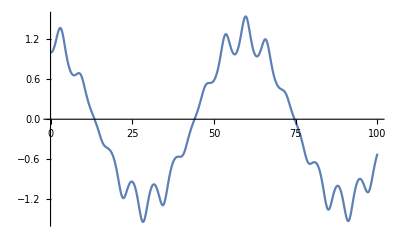

```mathematica
Plot[Evaluate[aa[t[]]/.s],{t[],0,100},PlotRange->All]
```

#### Solve (Approximation of small metric changes)

```mathematica
s=NDSolve[{({0,aa''[t[]],bb''[t[]],cc''[t[]]}//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues)==(wwww[{0,-ch},{0,-ch},a]//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues),((v[a]//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues)/.t[]->0)=={0,1,0,0}, (((CD[{0,-ch}]@v[a])//ToBasis[ch]//ToBasis[ch]//ToCanonical//ComponentArray//TraceBasisDummy//ToValues)/.t[]->0.25)=={0,0,0,0}},{aa,bb,cc},{t[],100}]
```

{{aa→InterpolatingFunction[…],bb→InterpolatingFunction[…],cc→InterpolatingFunction[…]}}

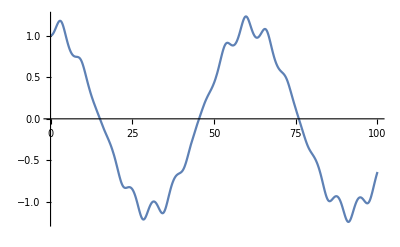

```mathematica
Plot[Evaluate[aa[t[]]/.s],{t[],0,100},PlotRange->All]
```